```mathematica
(* Burgers Vortex Sheet Solution of the Navier-Stokes Equation *)
```

```mathematica
V[x_,y_,z_] = {a x , b y +  S[z], -(a+b)z}; (* velocity field *)
P[x_,y_,z_] =  -a^2 x^2/2 - b^2 y^2/2- (a+b)^2 z^2 /2; (* pressure *)
(* Laplace operator *)
Lap[G_, R_] := D[G,{R[[1]],2}]+D[G,{R[[2]],2}] + D[G,{R[[3]],2}]; 
(* Navier-Stokes Equation *)
NSEq[VV_,PP_, R_] := Nu Lap[VV,R] - Grad[VV,R].VV -Grad[PP,R];
```

```mathematica
(* Incompressibility equation *)
```

```mathematica
Div[V[x,y,z],{x,y,z}]
```

0

```mathematica
Seq =S''[z] -> q z S'[z] + p S[z]
```

S''[z]→p S[z]+q z S'[z]

```mathematica
FullSimplify[NSEq[V[x,y,z],P[x,y,z], {x,y,z}]/.Seq]
```

{0,(-b+Nu p) S[z]+(a+b+Nu q) z S'[z],0}

```mathematica
Sol = {p->b/Nu,q-> -(a+b)/Nu}
```

{p→b/Nu,q→(-a-b)/Nu}

```mathematica
FullSimplify[NSEq[V[x,y,z],P[x,y,z], {x,y,z}]/.Seq/.Sol]
```

{0,0,0}

```mathematica
Seqsol = Seq/.Sol
```

S''[z]→(b S[z])/Nu+((-a-b) z S'[z])/Nu

```mathematica
DSolve[(b S[z])/Nu+((-a-b) z S'[z])/Nu==S''[z],S[z],z][[1]]
```

{S[z]→ⅇ^(-((a+b) z^2)/(2 Nu)) C[1] HermiteH[(-a-2 b)/(a+b),(√(a+b) z)/(√2 √Nu)]+ⅇ^(-((a+b) z^2)/(2 Nu)) C[2] Hypergeometric1F1[-(-a-2 b)/(2 (a+b)),1/2,((a+b) z^2)/(2 Nu)]}

```mathematica
absol =Solve[{(-a-2 b)/(a+b)==n, a+ b == c},{a,b}][[1]]
```

{a→2 c+c n,b→-c-c n}

```mathematica
V[x,y,z] /.absol
```

{(2 c+c n) x,(-c-c n) y+S[z],-c z}

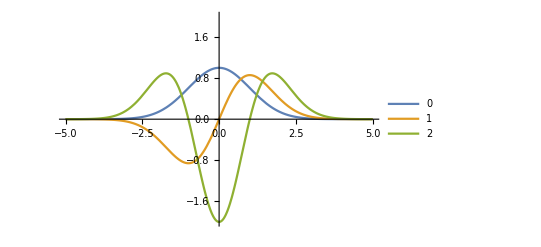

```mathematica
Show[Plot[{ⅇ^(-z^2/2)  HermiteH[0,z/(√2)],ⅇ^(-z^2/2)  HermiteH[1,z/(√2)],ⅇ^(-z^2/2)  HermiteH[2,z/(√2)]},{z,-5,5}, PlotRange->{-2,2},PlotLegends->{0,1,2}]]
```